Mathematical Techniques in Evolution and Ecology

# Equilibria and stability analysis – One-variable models (part I)

Based on Chapter 5 in Otto and Day (2007)

Spring Quarter 2015
Simon Aeschbacher
saeschbacher@ucdavis.edu

## Outline

### Goals

To determine the equilibria of a model with one variable

To determine the stability of equilibria

To find approximate values of an equilibrum (see part II, next week)

### Concepts

Equilibrium condition

Local stability analysis

Perturbation analysis (see part II, next week)

## Motivation and definitions

Finding the equilibria of a dynamical system is a very important step in analysing models. An equilibrium is a point at which a variable remains unchanged over time. In practice, this often tells us where the system of interest will end up. Equilibria can be stable or unstable.

### Definition 5.1: Equilibrium

A system at equilibrium (plural: equilibria) does not change over time. A particular value of a variable is called an equilibrium value if, when the variable is started at this value, the variable never changes.

At an equilibrium in a discrete-time model, n(t+1)=n(t) holds or, equivalently, Δn=n(t+1)-n(t)=0 for each variable

At an equilibrium in a continuous-time model, ⅆn/ⅆt=0 holds for each variable

Each of the three equations above is an equilibrium condition, i.e. a (set of) equation(s) that is (are) satisfied by the equilibria of a model

Remark: Whether, in a discrete-time model, you use the recursion or difference equation to determine the equilibria, does not matter. You should obtain the same answer. However, it is not generally true that the equilibria of a continuous-time differential equation are the same as the equilibria of the underlying discrete-time recursion of difference equation! This is because the two types of models make different assumptions about the possibility of concurrent events (see previous units).

### Definition 5.2: Stability

An equilibrium is locally stable if a system near the equilibrium approaches it (the equilibrium is then locally attracting)

An equilibrium is globally stable if a system approaches the equilibrium regardless of its initial position (the equilibrium is then globally attracting)

An equilibrium is unstable if a system near the equilibrium moves away from it (the equilibrium is said to be repelling)

## Finding an equilibrium

For notation, we will place a hat (^) over a variable to represent an equilibrium value of that variable, e.g. n̂ for an equilibrium value of n(t)

While the concept behind finding equilibria is straightforward, in practice it can be difficult or impossible to find them!

### Recipe 5.1: Finding an equilibrium n̂

Obtain the equilibrium condition from the dynamical equation:

In a discrete-time recursion equation, replace n(t+1) and n(t) with n̂. For example, the exponential growth model n(t+1)=R n(t) becomes n̂=R n̂.

In a discrete-time difference equation, replace n(t+1) with n̂ and set Δn=0. For example, the exponential growth model Δn=(R-1)n(t) becomes 0=(R-1)n̂.

In a continuous-time differential equation, replace n(t) with n̂ and set  ⅆn/ⅆt=0. For example, the exponential growth model ⅆn/ⅆt=r n(t) becomes 0=r n̂.

Solve the equilibrium condition for n̂. When cancelling a term from both sides of an equilibrium condition, check if that term could equal zero for some value of n̂. If so, that value of n̂ is an equilibrium of the model.

Check each equilibrium by plugging it back into the original dynamical equation and confirming that the system remains constant. Also check that each equilibrium is biologically valid (e.g. non-negative for counts, or between 0 and 1 for probabilities).

Remark: Remember in step 2 that we are solving for values of the variables that satisfy the equilibrium condition, not values of the parameters.

### Logistic model of population growth

Starting from the recursion equation

n (t+1)=n r t (1-(n t)/K)+n t,

let us construct the equilibrium condition and determine the equilibria.

### Back to our squirrels-on-campus example

Consider one of the toy models introduced in the first unit, in which we tracked the number of squirrels on campus, given that births, deaths through cyclists, and immigration from the Arboretum occur. For the case where immigration is the last event per time unit, we obtained the following dynamical equations:

n (t+1)=(b+1) (1-d) n(t)+m

Δn=-d n(t)+b(1-d)n(t)+m

ⅆn/ⅆt=b n(t)-d n(t)+m.

#### Exercise:

Write down the corresponding equilibrium conditions. These are implicit solutions for n̂. To obtain explicit solutions, solve the equilibrium conditions for n̂.

How do the parameters b, d, and m affect the number of squirrels at equilibrium?

Compare the discrete- with the continuous-time answer. What is different and why? In which model do you predict a lower equilibrium level of squirrels on campus?

### Haploid model of natural selection

Recall the general version of the discrete-time recursion equation,

p (t+1)=(W_A p(t))/(W_A p(t)+W_a(1-p(t))).

#### Exercise:

Write down the equilibrium condition

By solving for p̂, show that p̂=0 and p̂=1 are the two equilibria

Identify a special case of parameter values (i.e. fitnesses) that also satisfies the equilibrium condition

### Diploid model of natural selection

Recall the general form of the discrete-time recursion equation,

p (t+1)=((p(t))^2 W_AA+p(t)q(t)W_Aa)/((p(t))^2 W_AA+2p(t)q(t)W_Aa+(q(t))^2 W_aa).

Note that before proceeding, we have to express q(t) as 1-p(t) here. It would be wrong to leave q(t) in there and treat it as constant; it is a function of p(t)! The equilibrium condition therefore becomes

p̂=((p̂)^2 W_AA+p̂(1-p̂)W_Aa)/((p̂)^2 W_AA+2p̂(1-p̂)W_Aa+(1-p̂)^2 W_aa).

Solving for p̂ looks a bit tricky. Let us do this using a trick that often helps: Factoring the equation, focussing on one parameter at a time, simplifying all therms involving that parameter.

Having found the equilibria, let us check that ech equilibrium is biologically valid. Specifically, check what the equilibria are for

W_AA=0.6, W_Aa=0.2, and W_aa=1, and

W_AA=1, W_Aa=0.95, and W_aa=0.8.

Under which conditions will there be a so-called internal equilibrium, i.e. one for which 0<p̂<1 is satisfied?

### Rule 5.1: Simplifying inequalities

As a note of caution, when multiplying both sides of an inequality by a negative factor, one must reverse the inequality. Thus, a>b/c is equivalent to a c>b when c is positive, but is equivalent to a c<b when c is negative. If the sign of c is not known, it is safest to avoid multiplication by c!

Substracting terms from both sides of an inequality, however, never reverses the condition. Thus a>b/c is equivalent to a-b/c>0, regardless of the signs of these terms.

Similarly, one can always place terms over a common denominator without altering the condition. Thus, a-b/c>0 can be written as (a c-b)/c>0.

### When equilibria cannot be found explicitly

Sometimes, it is not possible to solve the equilibrium condition, i.e. the implicit solution for the equilibria cannot be turned into an explicit solution. For an example, see the example of the so-called Ricker model with migration in OD2007 (Subsection 5.2.3).

In such cases, we can use numerical methods (discussed in the previous unit) to solve for an equilibrium of interest.

Alternatively, one can try to find approximate values of the equilibria, as we will see later.

Equations that often cannot be solved explicitly are:

Mixtures of functions like exponentials, logarithms, or trigonometric (circular) functions (e.g. sine, cosine) plus polynomial functions. These belong to the category known as transcendental equations.

Even equilibrium conditions that are straightforward polynomial functions can be impossible to solve if the order of the polynomial is greater than 4.

## Determining stability

In practice, determining the stability properties of an equilibrium may become a routine, where you simply follow Recipe 5.3 below. However, let us together work through the steps that lead to this so-called local (or linear) stability analysis.

### Linear stability analysis

Determines whether an equilibrium is stable or unstable by approximating the dynamics of the system displaced slightly from the equilibrium

By definition, starting the system exactly at the equilibrium will lead to no change

Starting the system slightly off the equilibrium will lead to either a return to the equilibrium (if the equilibrium is stable) or to a further deviation from it (if the equilibrium is unstable)

To formalise these ideas, consider a population that starts at n(t), where n(t) is very close to an equilibrium n̂. Let us define the displacement from the equilibrium at time t as

ϵ(t):=n(t)-n̂.

If ϵ(t) increases in magnitude with time t, we have an unstable equilibrium. If it decreases in magnitude with t, the equilibrium is stable.

To decide, we need to write a recursion equation for the displacement ϵ(t), i.e. we want an equation of the form “ϵ(t+1)=function of ϵ(t)”.

This “function of ϵ(t)” may be complicated. The key is to approximate it using a Taylor series, assuming that ϵ(t) is small.

At time t+1, the displacement will be

ϵ(t+1)=n(t+1)-n̂ =f(n(t))-n̂.

This is not yet fromally a recursion in ϵ, as there is no ϵ(t) on the right-hand side. However, since n(t)=n̂+ϵ(t), we can write a propper recursion as

ϵ(t+1)=f(n(t))-n̂=f(n̂+ϵ(t))-n̂.

The tricky bit here is to deal with f(n̂+ϵ(t)), which may be a complicated function. The core idea is to exploit the fact that we are “close to the equilibrium”, i.e. that ϵ(t) is small. Expanding f(n̂+ϵ(t)) as a Taylor series around ϵ(t)=0 to first order yields

f(n̂+ϵ(t))=f(n̂)+((ⅆf(n))/ⅆn)|_(n=n̂)ϵ(t)+𝒪[(ϵ(t))^2].

To see why, set x=n(t)=n̂+ϵ(t) and a=n̂. The generic term ⅆf(x)/ⅆx|_(x=a)(x-a) translates to ⅆf(n)/ⅆn|_(n=n̂)ϵ(t), which is what we have just used.

Defining λ:=ⅆf(n)/ⅆn|_(n=n̂) and noting that f(n̂)=n̂ by definition, the recursion in ϵ(t) can therefore be approximated by

ϵ(t+1)=f(n̂+ϵ(t))-n̂≈f(n̂)+λ ϵ(t)-n̂=λ ϵ(t).

From this, it is easy to show (using iteration, for instance), that

ϵ(t)≈λ^t ϵ(0).

Exercise:

Describe the behaviour of the system near the equilibrium in terms of λ.

Relate this to the graphical interpretation we saw in the last unit, i.e. to a plot of n(t+1) as a function of n(t).

#### Exercise:

Analogously to the discrete-time version above, consider the continuous-time version and derive the differential equation for the displacement ϵ=n-n̂, i.e. find an equation of the form “ⅆϵ/ⅆt≈function of ϵ(t)”. Use (ⅆn(t))/ⅆt=f(n) for the underlying differential equation.

Describe the behaviour of the system near the equilibrium in terms of λ.

Relate this to the graphical interpretation we saw in the last unit, i.e. to a plot of (ⅆn(t))/ⅆt as a function of n(t).

What is different between the discrete-time version above and the continuous-time version here?

### Recipe 5.3: Performing a local stability analysis

#### Case A: Recursion equations in a discrete-time model

Consider n(t+1)=f(n), where f(n) is some function of n at time t. The local stability properties of any of the equilibria n̂ are determined as follows:

(1) Differentiate f(n) w.r.t. n to obtain ⅆf/ⅆn.

(2) Replace every instance of n in this derivative with the equilibrium value n̂ to obtain (ⅆf/ⅆn)|_(n=n̂).

(3) Define λ:=(ⅆf/ⅆn)|_(n=n̂).

(4) Determine the sign and magnitude of λ.

(5) Evaluate the stability of the equilibrium n̂ according to the following table:

```mathematica
decisionTableCaseATable
```

| λ < 0 | λ > 0
|λ| < 1 | n̂ is stable (oscillatory) | n̂ is stable (non-oscillatory)
|λ| > 1 | n̂ is unstable (oscillatory) | n̂ is unstable (non-oscillatory)

“Non-oscillatory” implies that the variable remains on the same side of the equilibrium over time. “Oscillatory” means that the variable alternates from side to side of the equilibrium.

#### Case B: Difference equations in a discrete-time model

Consider Δn=n(t+1)-n(t)=f(n), where f(n) is some function of n at time t. The local stability properties of any of the equilibria n̂ are determined as in Case A, with the exception of Step 3:

(3) Define λ:=(ⅆf/ⅆn)|_(n=n̂)-1.

#### Case C: Differential equations in a continuous-time model

Consider a differential equation ⅆn/ⅆt=f(n), where f(n) is some function of n at time t. The local stability properties of any of its equilibria n̂ are determined using Steps 1 and 2 above followed by:

(3) Define r:=(ⅆf/ⅆn)|_(n=n̂).

(4) Determine the sign of r.

(5) Evaluate the stability of the equilibrium n̂ according to the following table:

```mathematica
decisionTableCaseCTable
```

r < 0 | r > 0
n̂ is stable | n̂ is unstable

In one-variable, continuous-time models of the form discussed above, the variable never oscillates.

Remarks:

To avoid confusion, I suggest doing the stability analysis for discrete-time models always using the recursion equation, not the difference equation.

Steps 1 to 5 must be repeated for each equilibrium of interest.

### Logistic model of population growth

Starting from the discrete-time recursion equation

n(t+1)=f(n)=n(t)+r n(t)(1-(n(t))/K),

let us do a linear stability analysis following Recipe 5.3 for the two equilibria (n̂)_1=0 and (n̂)_2=K.

What happens if -1<r<0 and you start the population from

n(t)<K?

n(t)>K?

#### Exercise

Starting from the continuous-time differential equation

do a linear stability analysis for the equilibrium n̂=K.

What happens if

the population has a negative growth rate (r<0) and you start the population below the carrying capacity, i.e. from n(0)>K?

the population has a negative growth rate (r<0) and you start the population above the carrying capacity, i.e. from n(0)<K?

### Diploid model of natural selection

Starting from the discrete-time recursion equation

p (t+1)=((p(t))^2 W_AA+p(t)(1-p(t))W_Aa)/((p(t))^2 W_AA+2p(t)(1-p(t))W_Aa+(1-p(t))^2 W_aa),

let us do a stability analysis for the marginal equilibria (p̂)_1=0 and (p̂)_2=1, and for the internal equilibrium (p̂)_3 that we determined above.

## Problems

[Problem 5.6 in OD2007] Perform a local (linear) stability analysis of the haploid model of natural selection in discrete time, using the recursion equation

p(t+1)=(W_A p(t))/(W_A p(t)+W_a(1-p(t))).

(a) Determine when the equilibrium (p̂)_1=0 is stable.

(b) Determine when the equilibrium (p̂)_2=1 is stable.

(c) Check your results against a plot of p(t+1) against p(t) for a couple of numerical examples of W_A and W_a.

[Problem 5.10 in OD2007] Consider a haploid model of selection where selection in a marginal patch favours allele a: W_A=1-s and W_a=1. Adults migrate into the marginal patch from a more favourable area at rate m. Assume that these migrates all carry allele A, which is favoured in the core habitat. After migration, and assuming random mating, the frequency of the locally unfit allele A becomes p(t+1)=(1-m)p'+m, where p' is the frequency of allele A in the marginal patch after selection but before migration:

p'=(W_A p(t))/(W_A p(t)+W_a(1-p(t)))=((1-s)p(t))/((1-s)p(t)+(1-p(t))).

(a) Find the two equilibria of this model.

(b) What conditions must hold for the polymorphic equilibrium to be biologically valid?

(c) Examine the stability of the equilibrium p̂=1. Determine when allele a will disappear from the population when rare despite the fact that it is locally favoured by selection (W_a>W_A).

```mathematica
pHapRec[p_]:=(1-m)(1-s)/((1-s)p+(1-p))p+m
```

```mathematica
Simplify[(1-s)/((1-s)p+(1-p))p]
```

(p (-1+s))/(-1+p s)

```mathematica
Solve[(1-m)(1-s)/(1-p s)p+m==p,p]
```

{{p→1},{p→m/s}}

```mathematica
Simplify[Solve[s p+m p-s p^2==m,p]]
```

{{p→1},{p→m/s}}

```mathematica
Solve[(s p^2+s p+m p-m s p)/(1-s p)==m,p]
```

{{p→(-m-s+√(m^2+6 m s+s^2))/(2 s)},{p→-(m+s+√(m^2+6 m s+s^2))/(2 s)}}

## Initialisation cells

```mathematica
decisionTableCaseAData:={
{Column[{""}, Center], Column[{"λ < 0"},Center], Column[{"λ > 0"},Center]},

{Column[{"|λ| < 1"}, Center], Column[{"n̂ is stable (oscillatory)"},Center], Column[{"n̂ is stable (non-oscillatory)"},Center]},

{Column[{"|λ| > 1"}, Center], Column[{"n̂ is unstable (oscillatory)"},Center], Column[{"n̂ is unstable (non-oscillatory)"},Center]}
}
```

```mathematica
decisionTableCaseATable:=Grid[decisionTableCaseAData,Spacings->{1,1},ItemStyle->"Text",Alignment->Center,Frame->All,Background->{{None,None},{LightGray,None}}]
```

```mathematica
decisionTableCaseCData:={
{ Column[{"r < 0"},Center], Column[{"r > 0"},Center]},

{Column[{"n̂ is stable"},Center], Column[{"n̂ is unstable"},Center]}
}
```

```mathematica
decisionTableCaseCTable:=Grid[decisionTableCaseCData,Spacings->{1,1},ItemStyle->"Text",Alignment->Center,Frame->All,Background->{{None,None},{LightGray,None}}]
```

```mathematica
Simplify[(2p WAA+(1-2p)WAa)(p^2 WAA+2p(1-p)WAa+(1-p)^2 Waa)-(p^2 WAA+p(1-p)WAa)(2p WAA+(2-4p)WAa-(2-2p)Waa)]
```

p^2 WAa WAA+(-1+p) Waa ((-1+p) WAa-2 p WAA)

```mathematica
Manipulate[
Plot[
p WA/(WA p+Wa(1-p)),{p,0,1},
Frame->True,
FrameLabel->{"p(t)","p(t+1)"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14]
],
{{WA,0.5},0,1},{{Wa,0.5},0,1}
]
```

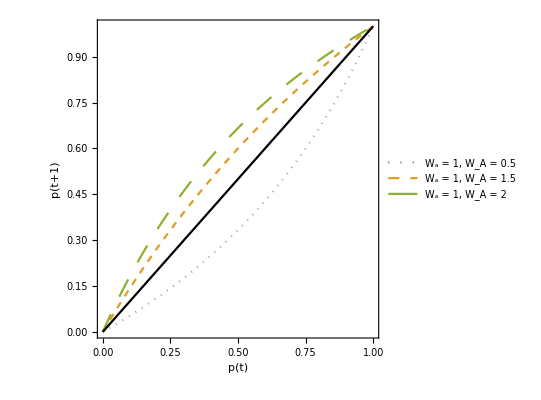

```mathematica
Plot[
{p WA/(WA p+Wa(1-p))/.{Wa->1,WA->0.5},p WA/(WA p+Wa(1-p))/.{Wa->1,WA->1.5},p WA/(WA p+Wa(1-p))/.{Wa->1,WA->2},p},{p,0,1},
PlotRange->{{0,1},{0,1}},
Frame->True,
FrameLabel->{"p(t)","p(t+1)"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14],
AspectRatio->1,
PlotStyle->{{Dotted},{Dashed},{Dashing[Large]},{Thickness[Small],Black}},
PlotLegends->{"W_a = 1, W_A = 0.5","W_a = 1, W_A = 1.5","W_a = 1, W_A = 2"}
]
```